```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Narrow resonance V=9, kres=0.5392022503575177-0.09990983772868195 ⅈ..... wide resonance V=2, kres=1.6568773873855651-1.4606098496557252 ⅈ*)
(*Remember we are using a potential V=Spherical well/(2mu) to make the mu dependence go away in the Sch. Eq.*)
a=1;
V0=9;
μ=1;
kres=0.5392022503575177-0.09990983772868195 ⅈ;
NSolve[z SphericalBesselJ[1,K[z]*a]SphericalHankelH1[0,z*a]-K[z] SphericalBesselJ[0,K[z]*a]SphericalHankelH1[1,z*a]==0 && 0<=Re[z]<10 && -10<Im[z]<5,{z}]
NSolve[z SphericalBesselJ[1,K[z]*a]SphericalHankelH2[0,z*a]-K[z] SphericalBesselJ[0,K[z]*a]SphericalHankelH2[1,z*a]==0 && -10<=Re[z]<10 && -10<Im[z]<5,{z}]
```

{{z→0.-3. ⅈ},{z→0.+3. ⅈ},{z→0.539202-0.0999098 ⅈ},{z→5.08598-1.5349 ⅈ},{z→8.62312-1.90916 ⅈ}}

{{z→-8.62312+1.90916 ⅈ},{z→-5.08598+1.5349 ⅈ},{z→-0.539202+0.0999098 ⅈ},{z→0.-3. ⅈ},{z→0.+3. ⅈ},{z→0.539202+0.0999098 ⅈ},{z→5.08598+1.5349 ⅈ},{z→8.62312+1.90916 ⅈ}}

```mathematica
K[u_]:=Sqrt[u^2+V0]
J[p_,p_]:= a^3/2 (SphericalBesselJ[1,p*a]^2-SphericalBesselJ[0,p*a]*SphericalBesselJ[2,p*a]);
J[p_,q_]:= a^2/(p^2-q^2)(q SphericalBesselJ[1,p*a]*SphericalBesselJ[0,q*a]-p SphericalBesselJ[0,p*a]*SphericalBesselJ[1,q*a]);
Λ[u_]:=I*8*Pi^2*μ*u/(1+I*2*V0*u*J[u,u]);
P1[u_]:=I/(u*a^2)(1/(K[u]*SphericalBesselJ[0,K[u]*a]*SphericalHankelH1[1,u*a]-u*SphericalBesselJ[1,K[u]*a]*SphericalHankelH1[0,u*a]));

NormInside[u_]:=(P1[u]^2*J[K[u],K[u]]+2*P1[u]*J[K[u],u]+J[u,u]);
NormOutside[u_]:=a^3/2*(P1[u]*SphericalBesselJ[1,K[u]*a]+SphericalBesselJ[1,u*a])^2/(SphericalHankelH1[1,u*a]^2) *(SphericalHankelH1[1,u*a]^2-SphericalHankelH1[0,u*a]*SphericalHankelH1[2,u*a]);
NormEnergy[u_]:=V0^2/(8Pi^2*μ*u) * (D[Λ[v](P1[u]*J[v,K[v]]+1/2*J[v,v])^2,v]/.v->u);
NormTotal[u_]:=NormInside[u]+NormOutside[u]-NormEnergy[u];
Γ[p_,u_]:=-V0/(2μ)*Sqrt[2/Pi](P1[u]*J[p,K[u]]+J[p,u](1-2I*V0*u*P1[u]*J[u,K[u]])/(1+2I*V0*u*P1[u]*J[u,K[u]]))
TFactorized[p_,q_,u_,ures_]:=2μ(Γ[p,-kres]*Γ[q,-kres])/(ures^2-u^2)*1/NormTotal[-kres];

A[q_,u_]:=V0/(K[u]^2-q^2)(u*SphericalBesselJ[1,q*a]*SphericalHankelH1[0,u*a]-q*SphericalBesselJ[0,q*a]*SphericalHankelH1[1,u*a])/(u*SphericalBesselJ[1,K[u]*a]*SphericalHankelH1[0,u*a]-K[u]*SphericalBesselJ[0,K[u]*a]*SphericalHankelH1[1,u*a]);
TExact[p_,q_,u_]:=-V0/(4*Pi^2*μ)(A[q,u]*J[p,K[u]]+(u^2-q^2)/(K[u]^2-q^2)J[p,q]);
```

```mathematica
AbsArgPlot[{TExact[k,k,k],TFactorized[k,k,k,kres]*(TExact[Re[kres],Re[kres],Re[kres]]/TFactorized[Re[kres],Re[kres],Re[kres],kres])},{k,0,10},PlotStyle->{{},{Dashed} },PlotLabel->"Solid=Exact T, Dashed=Factorized T",PlotRange->All]
AbsArgPlot[{TExact[k,k,k],1-8*Pi^2*I*μ*k*TExact[k,k,k]},{k,0,10},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
ComplexPlot3D[1/(z SphericalBesselJ[1,K[z]*a]SphericalHankelH1[0,z*a]-K[z] SphericalBesselJ[0,K[z]*a]SphericalHankelH1[1,z*a]),{z,-10-4I,10+4I}]
```

-Graphics3D-

-Graphics-

-Graphics-

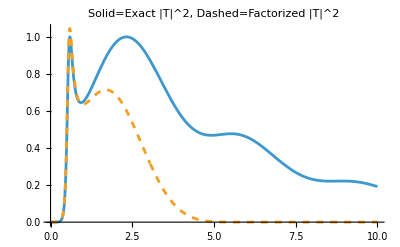

```mathematica
(* Try to Numerically Normalize *)
PsiUInside[r_,u_]:=P1[u]SphericalBesselJ[1,K[u]*r]+SphericalBesselJ[1,u*r]
PsiUOutside[r_,u_]:=(PsiUInside[a,u]/SphericalHankelH1[1,u*a])SphericalHankelH1[1,u*r]

(* <Psi|Psi> for inner and outer parts *)
NormInsideNumerical[u_]:=NIntegrate[r^2*PsiUInside[r,u]^2,{r,0,a},Method->"LocalAdaptive"]
NormOutsideNumerical[u_]:=NIntegrate[r^2*PsiUOutside[r,u]^2,{r,a,Infinity},Method->"LocalAdaptive"]

(* d/dv<Psi|U(v)|psi> (only the seperable part of U depends on v)*)
(* Compute <v|V|psi> *)
overlap[v_?NumericQ,u_]:=(-V0/(2μ))*Sqrt[2/Pi]*NIntegrate[r^2*PsiUInside[r,u]*SphericalBesselJ[1,v*r],{r,0,a},Method->"LocalAdaptive"]
(* Compute the seperable piece *)
matrixElement[v_?NumericQ,u_]:=Λ[v]*overlap[v,u]^2
(* Compute the derivative to give the norm *)
Needs["NumericalCalculus`"]
DerivativeNormNumerical[u_]:=(μ/u)*ND[matrixElement[v,u],v,u]

(* Total Norm *)
TotalNormNumerical[u_?NumericQ]:=TotalNormNumerical[u]=NormInsideNumerical[u]+NormOutsideNumerical[u]-DerivativeNormNumerical[u]

TFactorizedNumerical[p_,q_,u_,ures_]:=2μ(Γ[p,-ures]*Γ[q,-ures])/(ures^2-u^2)*1/TotalNormNumerical[-ures];
AbsArgPlot[{TExact[k,k,k],TFactorizedNumerical[-k,-k,-k,kres]},{k,0,10},PlotStyle->{{},{Dashed}},PlotLabel->"Solid=Exact T, Dashed=Factorized T",PlotRange->All]
AbsArgPlot[{Γ[k,0.5392022503575177+0.09990983772868195 ⅈ],1.5*Γ[k,-kres]},{k,0,10},PlotLabel->"Solid=Exact T, Dashed=Factorized T",PlotRange->All]
Plot[{(4Pi^2μ)^2k^2Abs[TExact[k,k,k]]^2,(4Pi^2μ)^2k^2Abs[TFactorizedNumerical[k,k,k,kres]]^2},{k,0,10},PlotStyle->{{},{Dashed} },PlotLabel->"Solid=Exact |T|^2, Dashed=Factorized |T|^2",PlotRange->All]
```

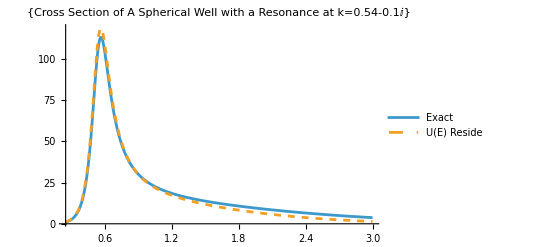

```mathematica
(* Construct the cross section by first getting the inverse K matrix, then making XS from that *)
KMatrixInverseFactorized[u_]:=Re[1/(TFactorizedNumerical[u,u,u,kres])]
KMatrixFactorized[u_]:=1/KMatrixInverseFactorized[u];
XSKMatrixFactorized[u_]:=(64 Pi^5 μ^2)*(2+1)(*(4Pi/p^2)(2L+1)*)*KMatrixFactorized[u]^2/(1+(4*Pi^2*μ*u*KMatrixFactorized[u])^2);

(* Exact cross section *)
XS[u_]:=(64Pi^5μ^2)*(2+1)*Abs[TExact[u,u,u]]^2;
XSFactorized[u_]:=(64Pi^5μ^2)*(2+1)*Abs[TFactorizedNumerical[u,u,u,kres]]^2;

Plot[{XS[z],XSFactorized[z]},{z,0.25,3},PlotStyle->{{},{Dashed}},PlotLabel->{"Cross Section of A Spherical Well with a Resonance at k=0.54-0.1ⅈ"},PlotLegends->{"Exact","U(E) Reside"},PlotRange->All]
```

```mathematica
(* Try to include Born term *)
TBorn[p_,q_]:=1/(2Pi^2)(-V0/(2μ))J[p,q]
SBorn[p_,q_]:=1-8*Pi^2*I*μ*p*TBorn[p,q]
AbsArgPlot[{TExact[k,k,k],TBorn[k,k]+SBorn[k,k]*TFactorizedNumerical[k,k,k,kres],TFactorizedNumerical[k,k,k,kres]},{k,0,10},PlotStyle->{{},{Dashed} ,{Dotted}},PlotLabel->"Solid=Exact T, Dashed=Factorized T",PlotRange->All]
```

-Graphics-

```mathematica
test = 2;
N[TExact[test,test,test]]
(TBorn[test,test]+TFactorizedNumerical[test,test,test,kres])
```

0.00214805-0.0122897 ⅈ

-0.013356+0.0102938 ⅈ

```mathematica
(* Try to include the "hard sphere" term that you get via Hadamards factorization. i.e. S = S_hs * (pole stuff)*)
Shs[p_]:=-SphericalHankelH2[1,p*a]/SphericalHankelH1[1,p*a] (*Shs=e^(2idelta_hs(k)*)
Ths[p_]:=(1-Shs[p])/(8*Pi^2*I*μ*p)

deltabg[p_]:=ArcTan[SphericalBesselJ[l,a*p]/SphericalBesselY[l,a*p]]
Sbg[p_]:=Exp[2*I*deltabg[p]]
Tbg[p_]:=Sin[deltabg[p]]*Exp[I*deltabg[p]]

AbsArgPlot[{TExact[k,k,k],Ths[k]+Shs[k]*TFactorizedNumerical[k,k,k,kres],TFactorizedNumerical[k,k,k,kres]},{k,0,10},PlotStyle->{{},{Dashed} ,{Dotted}},PlotLabel->"Solid=Exact T, Dashed=Factorized T + Hard Sphere, Dotted=Factorized T",PlotRange->All]
```

-Graphics-

```mathematica
NSolve[1-I*8*Pi^2*μ*z*TExact[z,z,z]==0 && 0>=Re[z]>-10 && 10>Im[z]>0,z]
```

{{z→-8.62312+1.90916 ⅈ},{z→-5.08598+1.5349 ⅈ},{z→-0.539202+0.0999098 ⅈ}}